```mathematica
(*Mathematica*)
```

```mathematica
gm0=1.56550000000000011
```

1.5655000000000001

```mathematica
N[gm0]
```

1.5655

```mathematica
gm1=1.5674967252475
```

1.5675

```mathematica
gm=Table[(1-p)*(gm0)+p*gm1,{p,-0.1,1.1,1/200}];
```

```mathematica
Length[gm]
N[gm]
```

241

{1.5653,1.56531,1.56532,1.56533,1.56534,1.56535,1.56536,1.56537,1.56538,1.56539,1.5654,1.56541,1.56542,1.56543,1.56544,1.56545,1.56546,1.56547,1.56548,1.56549,1.5655,1.56551,1.56552,1.56553,1.56554,1.56555,1.56556,1.56557,1.56558,1.56559,1.5656,1.56561,1.56562,1.56563,1.56564,1.56565,1.56566,1.56567,1.56568,1.56569,1.5657,1.56571,1.56572,1.56573,1.56574,1.56575,1.56576,1.56577,1.56578,1.56579,1.5658,1.56581,1.56582,1.56583,1.56584,1.56585,1.56586,1.56587,1.56588,1.56589,1.5659,1.56591,1.56592,1.56593,1.56594,1.56595,1.56596,1.56597,1.56598,1.56599,1.566,1.56601,1.56602,1.56603,1.56604,1.56605,1.56606,1.56607,1.56608,1.56609,1.5661,1.56611,1.56612,1.56613,1.56614,1.56615,1.56616,1.56617,1.56618,1.56619,1.5662,1.56621,1.56622,1.56623,1.56624,1.56625,1.56626,1.56627,1.56628,1.56629,1.5663,1.56631,1.56632,1.56633,1.56634,1.56635,1.56636,1.56637,1.56638,1.56639,1.5664,1.56641,1.56642,1.56643,1.56644,1.56645,1.56646,1.56647,1.56648,1.56649,1.5665,1.56651,1.56652,1.56653,1.56654,1.56655,1.56656,1.56657,1.56658,1.56659,1.5666,1.56661,1.56662,1.56663,1.56664,1.56665,1.56666,1.56667,1.56668,1.56669,1.5667,1.56671,1.56672,1.56673,1.56674,1.56675,1.56676,1.56677,1.56678,1.56679,1.5668,1.56681,1.56682,1.56683,1.56684,1.56685,1.56686,1.56687,1.56688,1.56689,1.5669,1.56691,1.56692,1.56693,1.56694,1.56695,1.56696,1.56697,1.56698,1.56699,1.567,1.56701,1.56702,1.56703,1.56704,1.56705,1.56706,1.56707,1.56708,1.56709,1.5671,1.56711,1.56712,1.56713,1.56714,1.56715,1.56716,1.56717,1.56718,1.56719,1.5672,1.56721,1.56722,1.56723,1.56724,1.56725,1.56726,1.56727,1.56728,1.56729,1.5673,1.56731,1.56732,1.56733,1.56734,1.56735,1.56736,1.56737,1.56738,1.56739,1.5674,1.56741,1.56742,1.56743,1.56744,1.56745,1.56746,1.56747,1.56748,1.56749,1.5675,1.56751,1.56752,1.56753,1.56754,1.56755,1.56756,1.56757,1.56758,1.56759,1.5676,1.56761,1.56762,1.56763,1.56764,1.56765,1.56766,1.56767,1.56768,1.56769,1.5677}

```mathematica
f[z_]:=-z*((ⅇ^(-2 ⅈ π gm[[i]])-ⅇ^(4 ⅈ π gm[[i]]))^(1/3))+z^2
```

```mathematica
(*v=JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001];*)
```

```mathematica
tm=ParallelTable[{i,Timing[ListPlot[JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001],ImageSize->{1920,1040},PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,DisplayFunction->False];]},{i,Length[gm]}]
```

{{1,{38.9516,Null}},{2,{36.6004,Null}},{3,{37.1171,Null}},{4,{29.2064,Null}},{5,{30.3476,Null}},{6,{30.8212,Null}},{7,{38.6683,Null}},{8,{41.2649,Null}},{9,{39.7166,Null}},{10,{37.5438,Null}},{11,{32.0455,Null}},{12,{35.135,Null}},{13,{35.0077,Null}},{14,{35.8447,Null}},{15,{31.4248,Null}},{16,{31.4211,Null}},{17,{31.9835,Null}},{18,{36.0613,Null}},{19,{32.6434,Null}},{20,{31.6877,Null}},{21,{31.7303,Null}},{22,{36.2181,Null}},{23,{33.2512,Null}},{24,{33.246,Null}},{25,{34.3346,Null}},{26,{37.6089,Null}},{27,{37.5798,Null}},{28,{38.8035,Null}},{29,{38.8817,Null}},{30,{38.5546,Null}},{31,{46.7532,Null}},{32,{35.3596,Null}},{33,{29.8467,Null}},{34,{35.6063,Null}},{35,{34.6704,Null}},{36,{33.8295,Null}},{37,{35.5894,Null}},{38,{28.8948,Null}},{39,{33.8519,Null}},{40,{34.3532,Null}},{41,{33.2298,Null}},{42,{35.3278,Null}},{43,{32.2165,Null}},{44,{35.8276,Null}},{45,{36.0016,Null}},{46,{33.3768,Null}},{47,{36.2875,Null}},{48,{36.1499,Null}},{49,{37.0456,Null}},{50,{31.3769,Null}},{51,{36.8901,Null}},{52,{37.0621,Null}},{53,{34.3557,Null}},{54,{33.2088,Null}},{55,{32.9625,Null}},{56,{32.2511,Null}},{57,{32.5135,Null}},{58,{31.5635,Null}},{59,{38.6609,Null}},{60,{39.4337,Null}},{61,{37.3797,Null}},{62,{29.6686,Null}},{63,{39.558,Null}},{64,{37.7573,Null}},{65,{39.7952,Null}},{66,{36.7651,Null}},{67,{38.8734,Null}},{68,{40.8775,Null}},{69,{40.4463,Null}},{70,{40.0939,Null}},{71,{37.0573,Null}},{72,{37.2346,Null}},{73,{36.2232,Null}},{74,{36.7685,Null}},{75,{36.9565,Null}},{76,{38.3574,Null}},{77,{43.5278,Null}},{78,{37.9108,Null}},{79,{39.0224,Null}},{80,{37.067,Null}},{81,{35.7613,Null}},{82,{37.6275,Null}},{83,{37.4529,Null}},{84,{36.4478,Null}},{85,{36.7678,Null}},{86,{36.8736,Null}},{87,{40.1596,Null}},{88,{39.0507,Null}},{89,{39.7064,Null}},{90,{44.8914,Null}},{91,{39.253,Null}},{92,{40.1793,Null}},{93,{38.8155,Null}},{94,{41.425,Null}},{95,{37.8835,Null}},{96,{41.072,Null}},{97,{43.0681,Null}},{98,{38.4669,Null}},{99,{38.2612,Null}},{100,{32.865,Null}},{101,{38.0363,Null}},{102,{36.3647,Null}},{103,{32.3133,Null}},{104,{42.6597,Null}},{105,{41.6499,Null}},{106,{34.1584,Null}},{107,{41.6603,Null}},{108,{41.5049,Null}},{109,{41.2169,Null}},{110,{44.2588,Null}},{111,{42.0828,Null}},{112,{39.6103,Null}},{113,{42.4863,Null}},{114,{44.2696,Null}},{115,{44.2099,Null}},{116,{45.8164,Null}},{117,{50.703,Null}},{118,{40.3086,Null}},{119,{39.5455,Null}},{120,{40.2983,Null}},{121,{40.4289,Null}},{122,{46.3976,Null}},{123,{46.9459,Null}},{124,{41.294,Null}},{125,{43.5796,Null}},{126,{47.6445,Null}},{127,{50.1114,Null}},{128,{51.0808,Null}},{129,{48.43,Null}},{130,{40.5385,Null}},{131,{35.9103,Null}},{132,{40.4793,Null}},{133,{40.7906,Null}},{134,{38.768,Null}},{135,{42.3024,Null}},{136,{36.7595,Null}},{137,{42.2989,Null}},{138,{43.3117,Null}},{139,{46.8306,Null}},{140,{44.5091,Null}},{141,{34.6364,Null}},{142,{43.0915,Null}},{143,{43.798,Null}},{144,{37.7019,Null}},{145,{38.342,Null}},{146,{33.1594,Null}},{147,{36.6955,Null}},{148,{43.3535,Null}},{149,{43.214,Null}},{150,{36.7281,Null}},{151,{40.4211,Null}},{152,{45.4022,Null}},{153,{35.8677,Null}},{154,{38.47,Null}},{155,{41.171,Null}},{156,{37.4772,Null}},{157,{36.5686,Null}},{158,{36.1176,Null}},{159,{49.0318,Null}},{160,{43.718,Null}},{161,{39.8359,Null}},{162,{40.4898,Null}},{163,{38.0785,Null}},{164,{35.9934,Null}},{165,{35.562,Null}},{166,{35.9323,Null}},{167,{33.2853,Null}},{168,{39.1222,Null}},{169,{52.8759,Null}},{170,{39.4178,Null}},{171,{38.613,Null}},{172,{41.5355,Null}},{173,{42.0187,Null}},{174,{44.9462,Null}},{175,{41.5813,Null}},{176,{37.1737,Null}},{177,{36.8232,Null}},{178,{42.517,Null}},{179,{49.9136,Null}},{180,{36.7069,Null}},{181,{37.0377,Null}},{182,{37.2907,Null}},{183,{40.2423,Null}},{184,{45.9987,Null}},{185,{45.9368,Null}},{186,{49.9938,Null}},{187,{39.4732,Null}},{188,{39.7306,Null}},{189,{41.3486,Null}},{190,{41.853,Null}},{191,{41.0136,Null}},{192,{48.7837,Null}},{193,{43.3461,Null}},{194,{41.011,Null}},{195,{40.5712,Null}},{196,{42.5151,Null}},{197,{52.4414,Null}},{198,{44.9189,Null}},{199,{55.5985,Null}},{200,{53.5863,Null}},{201,{58.5209,Null}},{202,{46.5763,Null}},{203,{39.2246,Null}},{204,{52.3197,Null}},{205,{43.5631,Null}},{206,{42.1694,Null}},{207,{50.7287,Null}},{208,{45.6817,Null}},{209,{44.7682,Null}},{210,{44.3187,Null}},{211,{43.1589,Null}},{212,{45.8217,Null}},{213,{48.0276,Null}},{214,{45.136,Null}},{215,{47.0198,Null}},{216,{52.3056,Null}},{217,{48.9834,Null}},{218,{44.4126,Null}},{219,{48.9068,Null}},{220,{50.9277,Null}},{221,{62.177,Null}},{222,{62.3108,Null}},{223,{39.8472,Null}},{224,{51.0753,Null}},{225,{52.7569,Null}},{226,{49.9429,Null}},{227,{41.9724,Null}},{228,{47.3687,Null}},{229,{48.6001,Null}},{230,{43.8679,Null}},{231,{51.3475,Null}},{232,{42.5952,Null}},{233,{39.6819,Null}},{234,{47.1634,Null}},{235,{40.5512,Null}},{236,{39.9075,Null}},{237,{49.8437,Null}},{238,{40.9559,Null}},{239,{40.6012,Null}},{240,{40.9911,Null}},{241,{40.5747,Null}}}

```mathematica
lt=ParallelTable[If[tm[[i,2,1]]>50,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]
```

{{117,50.703,1.56646},{127,50.1114,1.56656},{128,51.0808,1.56657},{169,52.8759,1.56698},{197,52.4414,1.56726},{199,55.5985,1.56728},{200,53.5863,1.56729},{201,58.5209,1.5673},{204,52.3197,1.56733},{207,50.7287,1.56736},{216,52.3056,1.56745},{220,50.9277,1.56749},{221,62.177,1.5675},{222,62.3108,1.56751},{224,51.0753,1.56753},{225,52.7569,1.56754},{231,51.3475,1.5676}}

```mathematica
lt150=N[ParallelTable[If[tm[[i,2,1]]>100,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]]
```

{}

```mathematica
lt200=N[ParallelTable[If[tm[[i,2,1]]>200,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]]
```

{}

```mathematica
(*All Timing results*)
```

```mathematica
lt0=Table[{gm[[i]],tm[[i,2,1]]},{i,Length[tm]}];
```

```mathematica
N[lt]
```

```mathematica
{{117.,50.702984,1.5664584281188},{127.,50.111362,1.566558264381175},{128.,51.08076,1.5665682480074126},{169.,52.875912,1.56697757668315},{197.,52.441353,1.5672571182178},{199.,55.598467,1.567277085470275},{200.,53.58631,1.5672870690965126},{201.,58.520914,1.56729705272275},{204.,52.319732,1.5673270036014624},{207.,50.728706,1.567356954480175},{216.,52.30563,1.5674468071163126},
{220.,50.927672,1.5674867416212626},{221.,62.177027,1.5674967252475},{222.,62.310782,1.5675067088737376},{224.,51.075313,1.5675266761262125},{225.,52.756937,1.56753665975245},{231.,51.347547,1.567596561509875}}
```

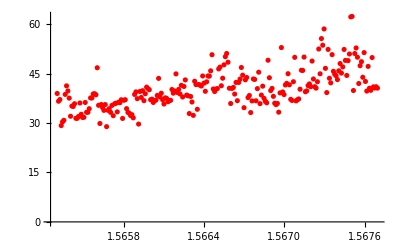

```mathematica
ListPlot[lt0,PlotStyle->Red,ImageSize->Full,PlotRange->All]
```

```mathematica
ListPointPlot3D[lt50,PlotStyle->Red,ImageSize->Full]
```

-Graphics3D-

```mathematica
st=ParallelTable[If[tm[[i,2,1]]<1,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]
```

{}

```mathematica
(*end*)
```